```mathematica
s4=({{0, 1, 0, 0}, {-1, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, -1, 0}});
```

```mathematica
x:=1/2 A(a1 E^(I(ψa+ϕa))+a1c E^(-I(ψa+ϕa)))+1/2 B(b1 E^(I(ψb+ϕb))+b1c E^(-I(ψb+ϕb)))
y:=1/2 A(a3 E^(I(ψa+ϕa))+a3c E^(-I(ψa+ϕa)))+1/2 B (b3 E^(I(ψb+ϕb))+b3c E^(-I(ψb+ϕb)))
```

```mathematica
xs=1/2 A(a2 E^(I(ψa+ϕa))+a2c E^(-I(ψa+ϕa)))+1/2 B(b2 E^(I(ψb+ϕb))+b2c E^(-I(ψb+ϕb)));
ys=1/2 A(a4 E^(I(ψa+ϕa))+a4c E^(-I(ψa+ϕa)))+1/2 B (b4 E^(I(ψb+ϕb))+b4c E^(-I(ψb+ϕb)));
```

```mathematica
a1=wx;
a1c=wx;
a2=(wxs-I/wx);
a2c=(wxs+I/wx);
a3=0;
a3c=0;
a4=0;
a4c=0;
b1=0;
b1c=0;
b2=0;
b2c=0;
b3=wy;
b3c=wy;
b4=(wys-I/wy);
b4c=(wys+I/wy);
```

```mathematica
ϕa=((νx+νy+2+η)/2) 2 π n+ϕa;
ϕb=((νx+νy+2-η)/2) 2 π n+ϕb;
```

```mathematica
a1=wx Cos[γ];
a1c=wx Cos[γ];
a2=(wxs+I/wx) Cos[γ];
a2c=(wxs-I/wx) Cos[γ];

a3=wy Sin[γ] Exp[-I α];
a3c=wy Sin[γ] Exp[I α];
a4=(wys+I/wy) Sin[γ] Exp[-I α];
a4c=(wys-I/wy) Sin[γ] Exp[I α];

b1=-Sin[γ]wx ;
b1c=-Sin[γ]wx ;
b2=-Sin[γ](wxs+I/wx);
b2c=-Sin[γ](wxs-I/wx);

b3=wy Cos[γ] Exp[-I α];
b3c=wy Cos[γ] Exp[I α];
b4=(wys+I/wy) Cos[γ] Exp[-I α];
b4c=(wys-I/wy)  Cos[γ] Exp[I α];
```

```mathematica
Simplify[x]
```

1/2 ⅇ^(-ⅈ (ϕa+ϕb+ψa+ψb)) wx (A ⅇ^(ⅈ (ϕb+ψb)) (1+ⅇ^(2 ⅈ (ϕa+ψa))) Cos[γ]-B ⅇ^(ⅈ (ϕa+ψa)) (1+ⅇ^(2 ⅈ (ϕb+ψb))) Sin[γ])

```mathematica
Fa=(Fx Exp[I(χx+n s/(2 R))]-(δ+η)/c Fy Exp[I(χy-n s/(2 R))])Exp[I s((νx+νy)/(2 R)+η/2)]
Fb=(Fx Exp[I(χx+n s/(2 R))]-(δ-η)/c Fy Exp[I(χy-n s/(2 R))])Exp[I s((νx+νy)/(2 R)-η/2)]
```

ⅇ^(ⅈ s (η/2+(νx+νy)/(2 R))) (ⅇ^(ⅈ ((n s)/(2 R)+χx)) Fx-(ⅇ^(ⅈ (-(n s)/(2 R)+χy)) Fy (δ+η))/c)

ⅇ^(ⅈ s (-η/2+(νx+νy)/(2 R))) (ⅇ^(ⅈ ((n s)/(2 R)+χx)) Fx-(ⅇ^(ⅈ (-(n s)/(2 R)+χy)) Fy (δ-η))/c)

```mathematica
(*Sextupole(hamiltonian part: x^2y...)*)
```

```mathematica
Hx:=2 x y; Hy:=x^2 - y^2; G:={0,Hy,0,-Hx};
```

```mathematica
eqA=Simplify[-I E^(-I(ψa+ϕa)){a1,a2c,a3c,a4c}.s4.G];
eqB=Simplify[-I E^(-I(ψb+ϕb)){b1c,b2c,b3,b4c}.s4.G];
```

```mathematica
Simplify[1/(4 π^2)Integrate[Integrate[eqA ⅇ^(1I (ϕa+ψa)) ⅇ^(2I (ϕb+ψb)),{ψa,0,2 π}],{ψb,0,2 π}]/.{a1->wx Cos[γ],a1c->wx Cos[γ],a3->wy Sin[γ],a3c->wy Sin[γ],b1->-Sin[γ]wx ,b1c->-Sin[γ]wx,b3->wy Cos[γ],b3c->wy Cos[γ]}]
```

1/8 ⅈ B^2 wx Cos[γ] (-wx^2-wy^2+(wx^2+3 wy^2) Cos[2 γ])

```mathematica
Simplify[1/(4 π^2)Integrate[Integrate[eqA ⅇ^(3 I (ϕa+ψa))ⅇ^(0I(ϕb+ψb)),{ψa,0,2 π}],{ψb,0,2 π}]/.{a1->wx Cos[γ],a1c->wx Cos[γ],a3->wy Sin[γ],a3c->wy Sin[γ],b1->-Sin[γ]wx ,b1c->-Sin[γ]wx,b3->wy Cos[γ],b3c->wy Cos[γ]}]
```

-1/4 ⅈ A^2 (wx^3 Cos[γ]^3-3 wx wy^2 Cos[γ] Sin[γ]^2)

```mathematica
Simplify[1/(4 π^2)Integrate[Integrate[eqA ⅇ^(0 I (ϕa+ψa))ⅇ^(3I(ϕb+ψb)),{ψa,0,2 π}],{ψb,0,2 π}]]
```

0

```mathematica
Simplify[1/(4 π^2)Integrate[Integrate[eqA ⅇ^(2 I (ϕa+ψa))ⅇ^(1 I(ϕb+ψb)),{ψa,0,2 π}],{ψb,0,2 π}]/.{a1->wx Cos[γ],a1c->wx Cos[γ],a3->wy Sin[γ],a3c->wy Sin[γ],b1->-Sin[γ]wx ,b1c->-Sin[γ]wx,b3->wy Cos[γ],b3c->wy Cos[γ]}]
```

1/4 ⅈ A B wx (wx^2+wy^2+(wx^2+3 wy^2) Cos[2 γ]) Sin[γ]

```mathematica
Simplify[1/(4 π^2)Integrate[Integrate[eqB ⅇ^(1ⅈ (ϕb+ψb)) ⅇ^(2ⅈ (ϕa+ψa)),{ψa,0,2 π}],{ψb,0,2 π}]]
```

0

```mathematica
Simplify[1/(4 π^2)Integrate[Integrate[eqB ⅇ^(2I(ϕb+ψb)) ⅇ^(1 I (ϕa+ψa)),{ψa,0,2 π}],{ψb,0,2 π}]]
```

1/2 ⅈ A B wx wy^2

```mathematica
Simplify[1/(4 π^2)Integrate[Integrate[eqB ⅇ^(3I(ϕb+ψb)) ⅇ^(0 I (ϕa+ψa)),{ψa,0,2 π}],{ψb,0,2 π}]]
```

0

```mathematica
DSolve[{(A[t])'==-(A[t])^2 h1 Sin[ϕa[t]],(ϕa[t])'==-A[t] h1 Cos[ϕa[t]]+n+1/3-δ+Δ},{A[t],ϕa[t]},t]
```

DSolve::derarg: The derivative operator Derivative[1] in A[t]' should act on the pure function.

```mathematica
NDSolve[{A'[t]==-h1 A[t]^2 Sin[ϕa[t]],ϕa'[t]==1/3+n-δ+Δ-h1 A[t] Cos[ϕa[t]],A[0]==1,ϕa[0]==0}/.{n->2,δ->.01,Δ->0,h1->1},{A[t],ϕa[t]},{t,0,4π}]
```

{{A[t]→InterpolatingFunction[…][t],ϕa[t]→InterpolatingFunction[…][t]}}

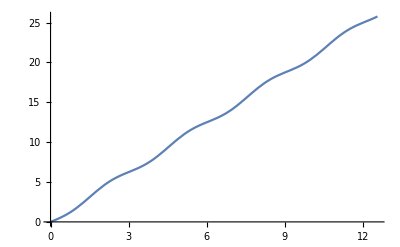

```mathematica
Plot[ϕa[t]/.{ϕa[t]->InterpolatingFunction[…][t]},{t,0,4π}]
```

```mathematica
(*oqtupole*)
```

```mathematica
Hx:=h2(3x^2y-y^3); Hy:=h2 (x^3-3x y^2); G:={0,-Hy,0,Hx};
```

```mathematica
eqA=Simplify[-I E^(-I(ψa+ϕa)){a1,a2c,a3c,a4c}.s4.G];
eqB=Simplify[-I E^(-I(ψb+ϕb)){b1c,b2c,b3,b4c}.s4.G];
```

```mathematica
Simplify[1/(4 π^2)Integrate[Integrate[eqA ⅇ^(1I (ϕa+ψa)) ⅇ^(-1I (ϕb+ψb)),{ψa,0,2 π}],{ψb,0,2 π}]]
```

3/32 ⅈ B ⅇ^(-ⅈ α) h2 (-B^2 (-wx^2 wy^2+ⅇ^(4 ⅈ α) wx^2 wy^2+ⅇ^(2 ⅈ α) (wx^4-wy^4))+2 A^2 (-wx^2 wy^2+ⅇ^(4 ⅈ α) wx^2 wy^2+ⅇ^(2 ⅈ α) (-wx^4+wy^4))-(2 A^2-B^2) (wx^2 wy^2+ⅇ^(4 ⅈ α) wx^2 wy^2+ⅇ^(2 ⅈ α) (wx^4+4 wx^2 wy^2+wy^4)) Cos[2 γ]) Sin[2 γ]

```mathematica
Simplify[1/(4 π^2)Integrate[Integrate[eqA ⅇ^(2 I (ϕa+ψa))ⅇ^(-0I(ϕb+ψb)),{ψa,0,2 π}],{ψb,0,2 π}]]
```

-3/8 ⅈ A h2 (wx^2 (A^2 wx^2-2 B^2 wy^2) Cos[γ]^4+2 (-3 A^2 wx^2 wy^2+B^2 (wx^4+wy^4)) Cos[γ]^2 Sin[γ]^2+wy^2 ((-2 B^2 wx^2+A^2 wy^2) Sin[γ]^4+2 B^2 wx^2 Sin[2 γ]^2))

```mathematica
Simplify[1/(4 π^2)Integrate[Integrate[eqA ⅇ^(-2 I (ϕa+ψa))ⅇ^(-0I(ϕb+ψb)),{ψa,0,2 π}],{ψb,0,2 π}]]
```

-1/8 ⅈ A^3 h2 (wx^4 Cos[γ]^4-6 wx^2 wy^2 Cos[γ]^2 Sin[γ]^2+wy^4 Sin[γ]^4)

```mathematica
Simplify[1/(4 π^2)Integrate[Integrate[eqA ⅇ^(0 I (ϕa+ψa))ⅇ^(2I(ϕb+ψb)),{ψa,0,2 π}],{ψb,0,2 π}]]
```

3/64 ⅈ A B^2 h2 (-(wx^2-wy^2)^2+(wx^4+6 wx^2 wy^2+wy^4) Cos[4 γ])

```mathematica
Simplify[1/(4 π^2)Integrate[Integrate[eqA ⅇ^(0 I (ϕa+ψa))ⅇ^(-2I(ϕb+ψb)),{ψa,0,2 π}],{ψb,0,2 π}]]
```

3/64 ⅈ A B^2 h2 (-(wx^2-wy^2)^2+(wx^4+6 wx^2 wy^2+wy^4) Cos[4 γ])

```mathematica
Simplify[1/(4 π^2)Integrate[Integrate[eqA ⅇ^(2 I (ϕa+ψa))ⅇ^(-2I(ϕb+ψb)),{ψa,0,2 π}],{ψb,0,2 π}]]
```

-3/64 ⅈ A B^2 ⅇ^(-2 ⅈ α) h2 (-ⅇ^(2 ⅈ α) wx^4+3 wx^2 wy^2-4 ⅇ^(2 ⅈ α) wx^2 wy^2+3 ⅇ^(4 ⅈ α) wx^2 wy^2-ⅇ^(2 ⅈ α) wy^4-4 (-1+ⅇ^(4 ⅈ α)) wx^2 wy^2 Cos[2 γ]+(wx^2 wy^2+ⅇ^(4 ⅈ α) wx^2 wy^2+ⅇ^(2 ⅈ α) (wx^4+4 wx^2 wy^2+wy^4)) Cos[4 γ])

```mathematica
Simplify[1/(4 π^2)Integrate[Integrate[eqA ⅇ^(0 I (ϕa+ψa))ⅇ^(0 I(ϕb+ψb)),{ψa,0,2 π}],{ψb,0,2 π}]]
```

-3/8 ⅈ A h2 (wx^2 (A^2 wx^2-2 B^2 wy^2) Cos[γ]^4+2 (-3 A^2 wx^2 wy^2+B^2 (wx^4+wy^4)) Cos[γ]^2 Sin[γ]^2+wy^2 ((-2 B^2 wx^2+A^2 wy^2) Sin[γ]^4+2 B^2 wx^2 Sin[2 γ]^2))

```mathematica
Simplify[1/(4 π^2)Integrate[Integrate[eqB ⅇ^(2ⅈ (ϕb+ψb)) ⅇ^(0ⅈ (ϕa+ψa)),{ψa,0,2 π}],{ψb,0,2 π}]]
```

-3/8 ⅈ B h2 wy^2 (-2 A^2 wx^2+B^2 wy^2)

```mathematica
Simplify[1/(4 π^2)Integrate[Integrate[eqB ⅇ^(2I(ϕb+ψb)) ⅇ^(-2 I (ϕa+ψa)),{ψa,0,2 π}],{ψb,0,2 π}]]
```

3/8 ⅈ A^2 B h2 wx^2 wy^2

```mathematica
Simplify[1/(4 π^2)Integrate[Integrate[eqB ⅇ^(1I(ϕb+ψb)) ⅇ^(-1 I (ϕa+ψa)),{ψa,0,2 π}],{ψb,0,2 π}]]
```

1/4 ⅈ A wx wy (1+Cos[2 γ]-2 ⅇ^(2 ⅈ ph) Sin[γ]^2)

```mathematica
FullSimplify[1/4 ⅈ  wx wy (1+Cos[2 γ]-2 ⅇ^(2 ⅈ ph) Sin[γ]^2)-(1/2  wx wy (Cos[ph] Cos[2 γ]+ⅈ Sin[ph]) (ⅈ Cos[ph]+Sin[ph]))]
```

wx wy Sin[2 ph] Sin[γ]^2

```mathematica
(*quadrup fringe*)
```

```mathematica
Hx:=-G2s(3x^2y+y^3)/12; Hy:=-G2s(x^3+3x y^2)/12;Hz=Gs x y; G:={0,ys Hz-Hy,0,Hx-xs Hz};
```

```mathematica
eqA=Simplify[-I E^(-I(ψa+ϕa)){a1,a2c,a3c,a4c}.s4.G];
eqB=Simplify[-I E^(-I(ψb+ϕb)){b1c,b2c,b3,b4c}.s4.G];
```

```mathematica
Simplify[1/(4 π^2)Integrate[Integrate[eqA ⅇ^(1I (ϕa+ψa)) ⅇ^(-1I (ϕb+ψb)),{ψa,0,2 π}],{ψb,0,2 π}]]
```

0

```mathematica
Simplify[1/(4 π^2)Integrate[Integrate[eqA ⅇ^(2 I (ϕa+ψa))ⅇ^(-0I(ϕb+ψb)),{ψa,0,2 π}],{ψb,0,2 π}]]
```

0

```mathematica
Simplify[1/(4 π^2)Integrate[Integrate[eqA ⅇ^(-2 I (ϕa+ψa))ⅇ^(-0I(ϕb+ψb)),{ψa,0,2 π}],{ψb,0,2 π}]]
```

-1/96 ⅈ A^3 G2s wx^4

```mathematica
Simplify[1/(4 π^2)Integrate[Integrate[eqA ⅇ^(0 I (ϕa+ψa))ⅇ^(2I(ϕb+ψb)),{ψa,0,2 π}],{ψb,0,2 π}]]
```

0

```mathematica
Simplify[1/(4 π^2)Integrate[Integrate[eqA ⅇ^(0 I (ϕa+ψa))ⅇ^(-2I(ϕb+ψb)),{ψa,0,2 π}],{ψb,0,2 π}]]
```

-1/32 ⅈ A B^2 wx^2 (G2s wy^2+4 Gs (-ⅈ+wy wys))

```mathematica
Simplify[1/(4 π^2)Integrate[Integrate[eqA ⅇ^(2 I (ϕa+ψa))ⅇ^(-2I(ϕb+ψb)),{ψa,0,2 π}],{ψb,0,2 π}]]
```

0

```mathematica
Simplify[1/(4 π^2)Integrate[Integrate[eqA ⅇ^(0 I (ϕa+ψa))ⅇ^(0 I(ϕb+ψb)),{ψa,0,2 π}],{ψb,0,2 π}]]
```

1/32 A ⅇ^(-2 ⅈ α) (-ⅈ ⅇ^(2 ⅈ α) wx^2 (A^2 G2s wx^2+2 B^2 wy (G2s wy+4 Gs wys)) Cos[γ]^4-ⅈ G2s (-A^2 (-1+ⅇ^(4 ⅈ α)) wx^2 wy^2+2 B^2 (-wx^2 wy^2+ⅇ^(4 ⅈ α) wx^2 wy^2+ⅇ^(2 ⅈ α) (wx^4-wy^4))) Cos[γ]^2 Sin[γ]^2+ⅈ ⅇ^(2 ⅈ α) wy^2 (2 B^2 wx (G2s wx+4 Gs wxs)+A^2 G2s wy^2) Sin[γ]^4+Gs (2 B^2 (ⅇ^(4 ⅈ α) wy^2-ⅈ ⅇ^(2 ⅈ α) (1+ⅇ^(2 ⅈ α)) wx wxs wy^2+ⅈ wx^2 (ⅈ+(1+ⅇ^(2 ⅈ α)) wy wys))+A^2 (-ⅇ^(4 ⅈ α) wy^2+ⅈ ⅇ^(2 ⅈ α) (2+ⅇ^(2 ⅈ α)) wx wxs wy^2+wx^2 (1-ⅈ (1+2 ⅇ^(2 ⅈ α)) wy wys))) Sin[2 γ]^2)

```mathematica
Simplify[1/(4 π^2)Integrate[Integrate[eqB ⅇ^(2ⅈ (ϕb+ψb)) ⅇ^(0ⅈ (ϕa+ψa)),{ψa,0,2 π}],{ψb,0,2 π}]]
```

0

```mathematica
Simplify[1/(4 π^2)Integrate[Integrate[eqB ⅇ^(2I(ϕb+ψb)) ⅇ^(-2 I (ϕa+ψa)),{ψa,0,2 π}],{ψb,0,2 π}]]
```

0

```mathematica
Simplify[1/(4 π^2)Integrate[Integrate[eqB ⅇ^(0I(ϕb+ψb)) ⅇ^(0 I (ϕa+ψa)),{ψa,0,2 π}],{ψb,0,2 π}]]
```

1/32 ⅈ B wy^2 (2 A^2 wx (G2s wx+4 Gs wxs)+B^2 G2s wy^2)

```mathematica
oqtupole
```

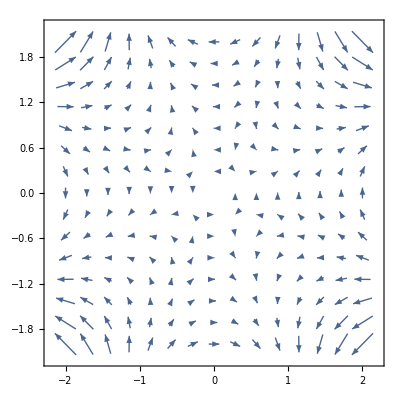

```mathematica
VectorPlot[{3x^2y-y^3,x^3-3x y^2},{x,-2,2},{y,-2,2}]
```

```mathematica
solenoid fringe
```

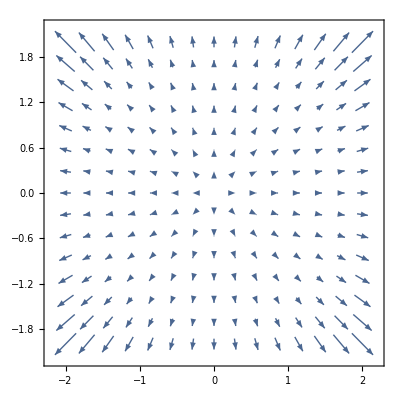

```mathematica
VectorPlot[{x^3+y^2 x,x^2 y+y^3},{x,-2,2},{y,-2,2}]
```

```mathematica
quadrupole fringe
```

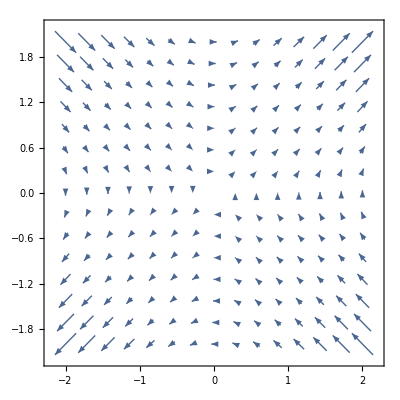

```mathematica
VectorPlot[{3x^2y+y^3,x^3+3x y^2},{x,-2,2},{y,-2,2}]
```

```mathematica
Hx:=h2(3x^2y-y^3); Hy:=h2 (x^3-3x y^2)+fr Exp[I wr s]; G:={0,Hy,0,-Hx};
```

```mathematica
Hx:=-h1 x; Hy:=h1 y; G:={0,Hy,0,-Hx};
```

```mathematica
eqA=Simplify[-I E^(-I(ψa+ϕa)){a1,a2c,a3c,a4c}.s4.G]
eqB=Simplify[-I E^(-I(ψb+ϕb)){b1c,b2c,b3,b4c}.s4.G]
```

-ⅈ ⅇ^(-ⅈ (ϕa+ψa)) (a1 ⅇ^(ⅈ s wr) fr-3/8 a3c ⅇ^(-3 ⅈ (ϕa+ϕb+ψa+ψb)) (A ⅇ^(ⅈ (ϕb+ψb)) (a1c+a1 ⅇ^(2 ⅈ (ϕa+ψa)))+B ⅇ^(ⅈ (ϕa+ψa)) (b1c+b1 ⅇ^(2 ⅈ (ϕb+ψb))))^2 (A ⅇ^(ⅈ (ϕb+ψb)) (a3c+a3 ⅇ^(2 ⅈ (ϕa+ψa)))+B ⅇ^(ⅈ (ϕa+ψa)) (b3c+b3 ⅇ^(2 ⅈ (ϕb+ψb)))) h2+a3c (1/2 A ⅇ^(-ⅈ (ϕa+ψa)) (a3c+a3 ⅇ^(2 ⅈ (ϕa+ψa)))+1/2 B ⅇ^(-ⅈ (ϕb+ψb)) (b3c+b3 ⅇ^(2 ⅈ (ϕb+ψb))))^3 h2+a1 ((1/2 A ⅇ^(-ⅈ (ϕa+ψa)) (a1c+a1 ⅇ^(2 ⅈ (ϕa+ψa)))+1/2 B ⅇ^(-ⅈ (ϕb+ψb)) (b1c+b1 ⅇ^(2 ⅈ (ϕb+ψb))))^3-3/8 ⅇ^(-3 ⅈ (ϕa+ϕb+ψa+ψb)) (A ⅇ^(ⅈ (ϕb+ψb)) (a1c+a1 ⅇ^(2 ⅈ (ϕa+ψa)))+B ⅇ^(ⅈ (ϕa+ψa)) (b1c+b1 ⅇ^(2 ⅈ (ϕb+ψb)))) (A ⅇ^(ⅈ (ϕb+ψb)) (a3c+a3 ⅇ^(2 ⅈ (ϕa+ψa)))+B ⅇ^(ⅈ (ϕa+ψa)) (b3c+b3 ⅇ^(2 ⅈ (ϕb+ψb))))^2) h2)

-ⅈ ⅇ^(-ⅈ (ϕb+ψb)) (b1c ⅇ^(ⅈ s wr) fr-3/8 b3 ⅇ^(-3 ⅈ (ϕa+ϕb+ψa+ψb)) (A ⅇ^(ⅈ (ϕb+ψb)) (a1c+a1 ⅇ^(2 ⅈ (ϕa+ψa)))+B ⅇ^(ⅈ (ϕa+ψa)) (b1c+b1 ⅇ^(2 ⅈ (ϕb+ψb))))^2 (A ⅇ^(ⅈ (ϕb+ψb)) (a3c+a3 ⅇ^(2 ⅈ (ϕa+ψa)))+B ⅇ^(ⅈ (ϕa+ψa)) (b3c+b3 ⅇ^(2 ⅈ (ϕb+ψb)))) h2+b3 (1/2 A ⅇ^(-ⅈ (ϕa+ψa)) (a3c+a3 ⅇ^(2 ⅈ (ϕa+ψa)))+1/2 B ⅇ^(-ⅈ (ϕb+ψb)) (b3c+b3 ⅇ^(2 ⅈ (ϕb+ψb))))^3 h2+b1c ((1/2 A ⅇ^(-ⅈ (ϕa+ψa)) (a1c+a1 ⅇ^(2 ⅈ (ϕa+ψa)))+1/2 B ⅇ^(-ⅈ (ϕb+ψb)) (b1c+b1 ⅇ^(2 ⅈ (ϕb+ψb))))^3-3/8 ⅇ^(-3 ⅈ (ϕa+ϕb+ψa+ψb)) (A ⅇ^(ⅈ (ϕb+ψb)) (a1c+a1 ⅇ^(2 ⅈ (ϕa+ψa)))+B ⅇ^(ⅈ (ϕa+ψa)) (b1c+b1 ⅇ^(2 ⅈ (ϕb+ψb)))) (A ⅇ^(ⅈ (ϕb+ψb)) (a3c+a3 ⅇ^(2 ⅈ (ϕa+ψa)))+B ⅇ^(ⅈ (ϕa+ψa)) (b3c+b3 ⅇ^(2 ⅈ (ϕb+ψb))))^2) h2)

```mathematica
Simplify[1/(4 π^2)Integrate[Integrate[eqA ⅇ^(1I (ϕa+ψa)) ⅇ^(-1I (ϕb+ψb)),{ψa,0,2 π}],{ψb,0,2 π}]/.{a1->wx Cos[γ],a1c->wx Cos[γ],a3->wy Sin[γ],a3c->wy Sin[γ],b1->-Sin[γ]wx ,b1c->-Sin[γ]wx,b3->wy Cos[γ],b3c->wy Cos[γ]}]
```

-3/32 ⅈ B h2 (-(2 A^2+B^2) (wx^4-wy^4)-(2 A^2-B^2) (wx^4+6 wx^2 wy^2+wy^4) Cos[2 γ]) Sin[2 γ]

```mathematica
Simplify[1/(4 π^2)Integrate[Integrate[eqA ⅇ^(1 I (ϕa+ψa))ⅇ^(-I(ϕb+ψb)),{ψa,0,2 π}],{ψb,0,2 π}]]
```

-1/2 ⅈ B h1 wx wy

```mathematica
Simplify[1/(4 π^2)Integrate[Integrate[eqA ⅇ^(2 I (ϕa+ψa))ⅇ^(-2I(ϕb+ψb)),{ψa,0,2 π}],{ψb,0,2 π}]/.{a1->wx Cos[γ],a1c->wx Cos[γ],a3->wy Sin[γ],a3c->wy Sin[γ],b1->-Sin[γ]wx ,b1c->-Sin[γ]wx,b3->wy Cos[γ],b3c->wy Cos[γ]}]
```

1/8 ⅈ A B^2 h2 wx wy (wx^2-wy^2) Sin[2 γ]

```mathematica
Simplify[1/(4 π^2)Integrate[Integrate[eqA ⅇ^(0 I (ϕa+ψa))ⅇ^(0 I(ϕb+ψb)),{ψa,0,2 π}],{ψb,0,2 π}]/.{a1->wx Cos[γ],a1c->wx Cos[γ],a3->wy Sin[γ],a3c->wy Sin[γ],b1->-Sin[γ]wx ,b1c->-Sin[γ]wx,b3->wy Cos[γ],b3c->wy Cos[γ]}]
```

-3/8 ⅈ A h2 (wx^2 (A^2 wx^2-2 B^2 wy^2) Cos[γ]^4+2 (-3 A^2 wx^2 wy^2+B^2 (wx^4+wy^4)) Cos[γ]^2 Sin[γ]^2+wy^2 ((-2 B^2 wx^2+A^2 wy^2) Sin[γ]^4+2 B^2 wx^2 Sin[2 γ]^2))